## Bayesian Statistics, Assignment for Tuesday, Nov. 19

## Reading

You can proceed through Chapter 11, which introduces gamma functions which are conjugate to Poisson distributions. The development in Chapter 11 is exactly analogous to Chapter 10 where you saw that beta functions are conjugate to binomial distributions. Alternatively, you can just study my handout on Bayesian conjugates. It is up to you, as long as you understand the take-home points from Chapters 10 and 11.

## For Problem Set 14 — The Mug Breakage Problem — With a Gamma Function Prior

I was looking ahead to Chapter 11 when I wrote Problem 4 on Exam 2. You might remember that it was called “The Mug Breakage Problem — But with an Exponential Prior.” Why was the exponential prior preparation for gamma distribution priors!? Well, here is the gamma distribution prior:

P(a)=β^α/(Γ(α))a^(α-1)e^-βa

For the exam, I chose α=1, and β=2. Plugging that in, you get

P(a)=2^1/(Γ(1))a^(1-1)e^(-2a)=2/(Γ(1))a^0 e^(-2a)=2/(Γ(1))e^(-2a)

and it happens that Γ(1)=1 so this simplifies to

P(a)=2 e^(-2a)

which is exactly what I gave for the prior on that exam problem. So you were already warming up to Bayesian conjugates by doing a special case.

## 1. Tabulating the Gamma Function

Now here is something confusing: this whole thing that we are looking at,

P(a)=β^α/(Γ(α))a^(α-1)e^-βa,

I have been calling  “the gamma function.” 

It happens that the thing in the denominator is needed to normalizes this gamma function is also called “the gamma function.” What a pain. To disambiguate this annoying terminology collision I will try to be better and do what statisticians do which is to call the whole thing “the gamma distribution.” 

Then when I am referring to the gamma function, I should be just referring to what is in the denominator.

Here is a graph of the gamma function:

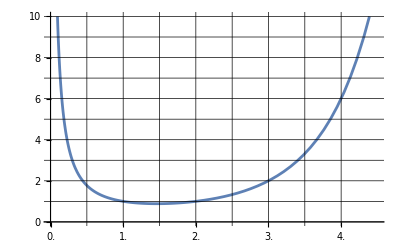

```mathematica
Plot[Gamma[x],{x, 0, 4.5},PlotRange->{{0.0,4.5},{0,10}}, GridLines->{Range[0,4,0.5],Range[0,10,1]}, GridLinesStyle->Directive[Black],Ticks->{Range[0.0,4.5,0.5],Range[0,10,1]}]
```

(a) Examining this graph, please write down, what is

Γ(1)=

Γ(2)=

Γ(3)=

Γ(4)=

(b) If I told you that 

Γ(5)=24

Γ(6)=120

Γ(7)=720

could you make a guess as to what Γ(n+1) is?

Γ(n+1)=

For the formula you just discovered and checked against the above 7 cases, you can see why the gamma function is thought of as a generalization of the factorial function. The factorial function is only defined for integer values of n. Γ(n+1) has a value for all values of n, except at 0 and at negative integers, where it blows up.

## 2. Exploring the Gamma Distribution

(a) Coming back to the gamma distribution

P(a)=β^α/(Γ(α))a^(α-1)e^-βa

Simplify this for the special case α=2 and β=3. Use what you found for Γ(2) in Problem 1 to finish the simplification.


P(a)=

I will have Mathematica plot the function you found:

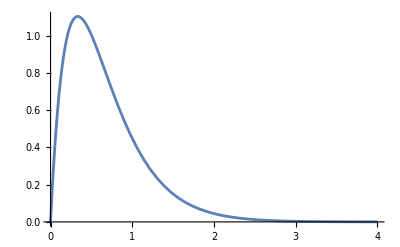

```mathematica
gamma[a_,α_,β_]:=β^α/Gamma[α] a^(α-1)Exp[-βa];
Plot[gamma[a,2,3],{a,0,4}]
```

(b) The junk out front is just there to normalize the function to have total area 1 and it might be plausible that the function above indeed has area 1.If I had asked you to simplify the exact same function, except without the normalization factor, you’d be simplifying  Q(a)=a^(α-1)e^-βa. Please simplify that for the same special case, α=2 and β=3:

 Q(a)=

(c) What is the area under the curve of Q(a)?



(d) A bit of jargon is that since these are the same function of a, but with different factors out front (which are independent of a), we say these functions are proportional, and we write

Q(a)∝P(a)

the little fish that means proportionality looks an awful lot like an α, so be careful.

Is (Q(a))/(∫_0^∞ Q(b)db) proportional to Q(a)?


(e) What is the area under the curve of the function (Q(a))/(∫_0^∞ Q(b)db)?

## 3. Some Likelihoods

The formula you need for likelihood in the case of Poisson distributions was on p. 59 of Young:

-Graphics-

We observe the kitchen for two weeks.

(a) Write down the likelihood of having n=4 mugs broken in the first week.


(b) Repeat, but with n=1 mug for the second week.


(c) Take the product of what you got in (a) and (b).


P(data|a)=

## 4. The Posterior

In 2(a) you wrote down the prior, P(a).

In 3(c) you wrote down the posterior, P(data|a)

(a) By Bayes theorem, you know that the posterior is proportional to  P(data|a)P(a). The proportionality constant is something I often call “denominator” and it is

∫_0^∞ P(data|b)P(b)db

so what Bayes theorem actually says is

P(a|data)=(P(data|a)P(a))/(∫_0^∞ P(data|b)P(b)db)

Just ignore that stinking denominator for a second. It doesn’t depend on a, so it only changes the overall vertical scale of the function. Pretend for just a second that it isn’t there, and if it weren’t write simplify:

P_(pretend version)(a|data)=P(data|a)P(a)




(e) In Problem Set 11, we had one of those boxcar-shaped priors. In this problem, we are going to have an exponential prior: 

P(a)=2 e^(-2a)

The formula for the posterior is: P(a|data)=(P(data|a) * P(a))/(∫_0^∞ P(data|a) * P(a)da). For this part, we will just deal with the numerator. Then in the next part, we will deal with the denominator. Simplify the numerator as much as you can


P(data|a) * P(a)=




(f) I am going to have Mathematica plot the function that you got in the previous part. And I am going to have Mathematica do the integral in the denominator.

```mathematica
likelihood[a_]:=a^6 Exp[-3a]/12;
prior[a_]:=2Exp[-2a];
```

0.0015

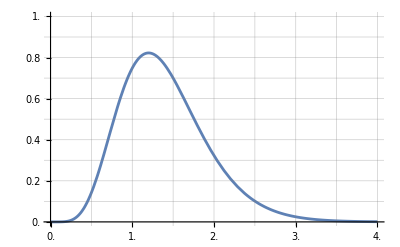

```mathematica
denominator = Round[Integrate[likelihood[a]*prior[a], {a, 0, Infinity}],0.0001]
Plot[likelihood[a]prior[a]/denominator,{a, 0, 4}, PlotRange->{{0, 4},{0,1}}, Ticks->{Range[0,4,0.5], Range[0.0,1,0.1]}, GridLines->{Range[0,4,0.5], Range[0.0,1,0.1]}]
```

So what does that leave you to do for this part!? Interpretation! Clearly the most probable mug breakage rate is somewhere between 1 and 1.5, but lots of other ranges of a are still non-negligible. Shade the region of the graph that tells you the probability that the mug breakage rate is between 2 and 2.5.

(g) Now that you have shaded the region of the graph that tells you the mug breakage rate is between 2 and 2.5, what is its width, what is its average height, and what is its area? When you are estimating the average height, one decimal place is plenty good for our purposes.




(h) Convert the area that you got in the previous part to a percentage.


I HOPE THIS EXAM WAS FUN! It was fun for me to write, because all of you are getting to the point that we can do problems quite similar to problems that matter in the real world. Each of these problems is building my intuition too!